index of start:(10,15 )

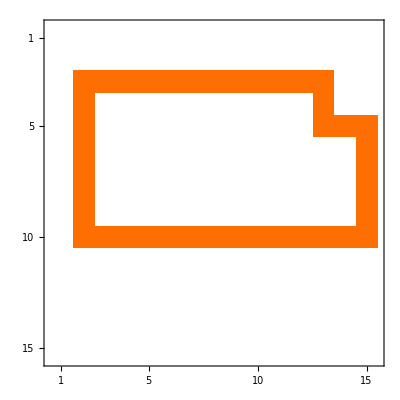

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(3,2 )

(3,13 )

(5,13 )

(5,15 )

(10,2 )

(10,15 )

```mathematica
M = Table[0, {i, 1,15}, {j, 1,15}];
(*зарисовка цикла*)
For[i = 0, i <11, ++i,
M[[3,2 + i]]=1;
]
For[i = 0, i <2, ++i,
M[[3 + i,13]]=1;
]
For[i = 0, i <2, ++i,
M[[5,13 + i]]=1;
]
For[i = 0, i <6, ++i,
M[[5+i,15]]=1;
]
For[i = 0, i <13, ++i,
M[[10,2+i]]=1;
]
For[i = 0, i <7, ++i,
M[[3+i,2]]=1;
]
(*M[[3,2]]=1;
M[[3,13]]=1;
M[[5,13]]=1;
M[[5,15]]=1;
M[[10,15]]=1;
M[[10,2]]=1;
M[[3,2]]=1;*)
IndexI = 0;
IndexJ = 0;
arrayI = Table[0,{k,225}];
arrayJ = Table[0,{k,225}];
For[i = 1, i ≤ 15, i++,
For[j = 1, j ≤ 15, j++,
If[M[[i,j]] == 1,IndexI =i; IndexJ = j; Break , 0];
]
]
Print ["index of start:(",IndexI,",",IndexJ ")" ]
MatrixPlot[M]
MatrixForm[M]
index = 1;
For[i = 1, i ≤ 15, i++,
For[j = 1, j ≤ 15, j++,
If[M[[i,j]] == 1,
If[i< 15 && i > 1,
If[M[[i + 1,j] ]!=M[[i - 1,j] ],arrayI[[index]] = i; arrayJ[[index++]] = j
] ,If[i == 1&&  M[[i + 1,j] ]==M[[i ,j] ] , arrayI[[index]] = i; arrayJ[[index++]] = j ,  If[i == 15&&  M[[i - 1,j] ]==M[[i ,j] ] , arrayI[[index]] = i; arrayJ[[index++]] = j]
]
]
]
]
]
For[i = 1, i < index, i++,
 Print ["(",arrayI[[i]],",",arrayJ [[i]]")" ]
]
```